## Bounds on Scalar-Tensor Theory From GW1510914

```mathematica
data1=Import[NotebookDirectory[]<>"/overall_post_150914.csv","CSV"] (*Posterior containing cos_theta_inc,luminosity distance,right ascension, declination, m1_det,m2_det,spin_1,spin_2,cos_tilt1,cos_tilt2 respectively.*)
```

{{-0.901839,438.878,1.6919,-1.27538,36.5582,34.2617,0.394141,0.0330915,-0.213274,-0.961184},16330,{-0.960167,432.955,1.12358,-1.17649,41.3096,17,0.11068,0.423524,0.156429,0.304489}}
 |  |  |  |

```mathematica
data2=Import[NotebookDirectory[]<>"/-1pn-phase-only-beta.csv","CSV"]  (*PPE beta*)
data3=Import[NotebookDirectory[]<>"/-1pn-amp-only-alpha.csv","CSV"] (*PPE alpha*)
```

{{0.0000835696},{0.0000857924},{0.000088643},{0.0000848591},{0.000083665},{0.0000983828},{0.000086322},{0.0000870475},16317,{0.0000879308},{0.000088384},{0.0000877578},{0.0000874088},{0.0000947909},{0.000093868},{0.0000892042}}
 |  |  |  |

{{0.0161963},{0.0168031},{0.0158669},{0.0167165},{0.0161385},{0.0154321},{0.0171932},{0.0157346},{0.016273},16314,{0.0160535},{0.0162675},{0.0158457},{0.0161739},{0.0160464},{0.0161101},{0.0159761},{0.015686},{0.0166971}}
 |  |  |  |

```mathematica
data4=Import[NotebookDirectory[]<>"/-1pn-combined-correlated-beta.csv","CSV"] (*PPE alpha*)
```

{{0.0000904525},{0.0000931781},{0.0000958978},{0.0000920836},{0.0000906122},{0.000105868},{0.0000937855},{0.0000940669},16316,{0.0000980632},{0.0000950742},{0.00009579},{0.0000949968},{0.0000945403},{0.000102339},{0.000101574},{0.0000968086}}
 |  |  |  |

```mathematica
Length[data3]
```

16332

```mathematica
χ1=data1[[All,7]]; (*Dimensionles spin parameter*)
χ2=data1[[All,8]];
```

```mathematica
DL=data1[[All,2]]*10^6*3.261636*tyear/.tyear->3.1536*10^7
```

{4.51425×10^16,6.31727×10^16,5.00873×10^16,3.92708×10^16,5.55192×10^16,2.70936×10^16,4.16762×10^16,5.46719×10^16,16316,3.99475×10^16,5.08785×10^16,3.9558×10^16,5.22933×10^16,3.93816×10^16,5.38142×10^16,3.86166×10^16,4.45333×10^16}
 |  |  |  |

```mathematica
Clear[z]
```

```mathematica
Clear[z1,z2]
```

```mathematica
$Assumptions:=z1<1
```

```mathematica
A=Series[(ωM(1+z1)^3+ωΛ)^(-1/2),{z1,0,1}]//Normal
```

-(3 z1 ωM)/(2 (ωM+ωΛ)^(3/2))+1/(√(ωM+ωΛ))

```mathematica
B=(1+z)/H0 Integrate[A,{z1,0,z}]//Expand
```

-(3 z^2 ωM)/(4 H0 (ωM+ωΛ)^(3/2))-(3 z^3 ωM)/(4 H0 (ωM+ωΛ)^(3/2))+z/(H0 √(ωM+ωΛ))+z^2/(H0 √(ωM+ωΛ))

```mathematica
B2=Series[B,{z,0,2}]//Normal
```

z/(H0 √(ωM+ωΛ))+(z^2 (ωM+4 ωΛ))/(4 H0 (ωM+ωΛ)^(3/2))

```mathematica
Clear[z]
```

```mathematica
z=z/.Solve[B2-Dl==0,z][[2]]
```

(2 H0 (ωM+ωΛ)^(3/2) (-1/(H0 √(ωM+ωΛ))+√(1/(H0^2 (ωM+ωΛ))+(Dl (ωM+4 ωΛ))/(H0 (ωM+ωΛ)^(3/2)))))/(ωM+4 ωΛ)

```mathematica
z2=z/.{Dl->DL,ωM->0.3111,ωΛ->0.6889,α->0,H0->2.2683085*10^-18}
```

{0.0954171,0.130282,0.105138,0.0837063,0.115676,0.0588054,0.0885261,0.114042,0.0956385,16314,0.0807763,0.0850656,0.106683,0.0842835,0.109436,0.083929,0.112384,0.0823902,0.0942106}
 |  |  |  |

```mathematica
m1=data1[[All,5]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6 
(*Ligo posterior gives mass in detector frame. We have to convert it source frame*)
```

{0.000164382,0.000172434,0.000186598,0.000166746,0.000160002,0.000214392,0.000176635,0.000174911,16317,0.000181667,0.000185522,0.000178181,0.000180393,0.000202519,0.000202124,0.000185951}
 |  |  |  |

```mathematica
m2=data1[[All,6]]/(1+z2)*tsolar/.tsolar->4.925491*10^-6
```

{0.000154056,0.000150252,0.00013417,0.000166077,0.000153064,0.000129181,0.000164308,0.000137253,16316,0.000137974,0.000135998,0.000145104,0.000141122,0.000145081,0.000126583,0.000133266,0.000149862}
 |  |  |  |

```mathematica
η=(m1*m2)/(m1+m2)^2;
```

```mathematica
βppE=data2[[All,1]](*1-sigms upper bound*)
αppE=data3[[All,1]](*1-sigma upper bound*)
```

{0.0000835696,0.0000857924,0.000088643,0.0000848591,0.000083665,0.0000983828,0.000086322,0.0000870475,16316,0.0000904535,0.0000879308,0.000088384,0.0000877578,0.0000874088,0.0000947909,0.000093868,0.0000892042}
 |  |  |  |

{0.0161963,0.0168031,0.0158669,0.0167165,0.0161385,0.0154321,0.0171932,0.0157346,0.016273,0.0157228,16312,0.0159456,0.0160535,0.0162675,0.0158457,0.0161739,0.0160464,0.0161101,0.0159761,0.015686,0.0166971}
 |  |  |  |

```mathematica
βppEcomb=data4[[All,1]](*1-sigma upper bound*)
```

{0.0000904525,0.0000931781,0.0000958978,0.0000920836,0.0000906122,0.000105868,0.0000937855,0.0000940669,0.0000908726,16315,0.0000980632,0.0000950742,0.00009579,0.0000949968,0.0000945403,0.000102339,0.000101574,0.0000968086}
 |  |  |  |

```mathematica
s1=(1+√(1-χ1^2))/2 (*Sensitivity in scalar-tensor*)
s2=(1+√(1-χ2^2))/2
```

{0.959525,0.853652,0.999912,0.996693,0.957429,0.994472,0.998851,0.990716,0.999987,16314,0.947075,0.987879,0.908264,0.999229,0.999989,0.99078,0.686606,0.999659,0.996928}
 |  |  |  |

{0.999726,0.950278,0.977818,0.995736,0.971108,0.999458,0.958939,0.958736,0.962357,16314,0.824445,0.59088,0.981882,0.999959,0.999904,0.999962,0.914585,0.975786,0.952943}
 |  |  |  |

```mathematica
ϕdotSquared=Abs[-1792/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*βppE]
```

{3.77978×10^9,2.74936×10^9,1.82265×10^7,7.77365×10^10,2.52299×10^9,8.90426×10^6,1.51335×10^8,3.14247×10^7,16316,4.35187×10^6,5.58772×10^7,3.41965×10^7,4.00642×10^7,4.83843×10^7,1.11556×10^8,1.14906×10^7,3.0859×10^7}
 |  |  |  |

```mathematica
√Mean[ϕdotSquared]//ScientificForm (*A rough estimat of phidot*)
```

8.17741×10^5

```mathematica
ϕdotSquaredamp=Abs[-48/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*αppE]
```

{1.96217×10^10,1.44236×10^10,8.73889×10^7,4.1018×10^11,1.30359×10^10,3.74117×10^7,8.0738×10^8,1.5215×10^8,16316,2.0964×10^7,2.69717×10^8,1.6762×10^8,1.96224×10^8,2.38865×10^8,5.03618×10^8,5.1433×10^7,1.54718×10^8}
 |  |  |  |

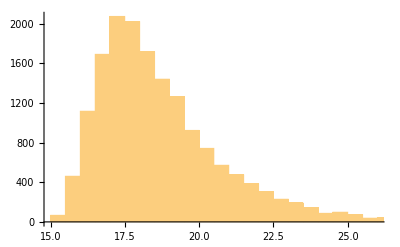

```mathematica
Histogram[Log[ϕdotSquared]]
```

```mathematica
ϕdotSquaredcomb=Abs[-1792/5*η^(-2/5)/((m1*s1)-(m2*s2))^2*βppEcomb]
```

{4.09108×10^9,2.98605×10^9,1.97183×10^7,8.43546×10^10,2.73249×10^9,9.58174×10^6,1.6442×10^8,3.39587×10^7,16316,4.71798×10^6,6.04166×10^7,3.7062×10^7,4.3369×10^7,5.23318×10^7,1.2044×10^8,1.24339×10^7,3.34897×10^7}
 |  |  |  |

ϕ̇ from phase correction:

```mathematica
LogSquaredϕdotPhase=Log[ϕdotSquared] (*This is Log of sigma_(alpha^2)*)
```

{22.0529,21.7346,16.7184,25.0766,21.6487,16.002,18.835,17.2631,20.4928,16314,16.8605,15.2861,17.8387,17.3476,17.506,17.6947,18.53,16.257,17.2449}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotPhase]
```

15.0147

```mathematica
Max[LogSquaredϕdotPhase]
```

35.8808

```mathematica
𝒟logϕHist=HistogramDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕHist2=PDF[𝒟logϕHist,x];
```

```mathematica
𝒟logϕHist3[x_]=𝒟logϕHist2;
```

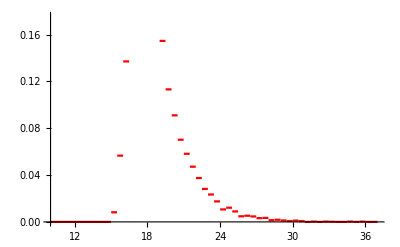

```mathematica
Plot1=Plot[𝒟logϕHist3[x],{x,10,37},PlotStyle->Red]
```

```mathematica
𝒟logϕdotSq=SmoothKernelDistribution[LogSquaredϕdotPhase]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSq2=PDF[𝒟logϕdotSq,x]
```

Piecewise[{{InterpolatingFunction[…][x], 13.7978≤x≤37.0978}, {0, True}}]

```mathematica
𝒟logϕdotSq3[x_]=𝒟logϕdotSq2
```

Piecewise[{{InterpolatingFunction[…][x], 13.7978≤x≤37.0978}, {0, True}}]

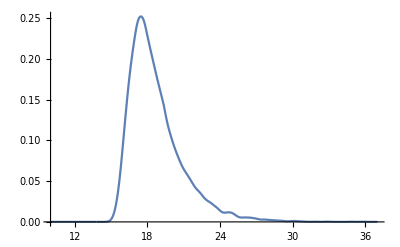

```mathematica
Plot2=Plot[𝒟logϕdotSq3[x],{x,10,37}]
```

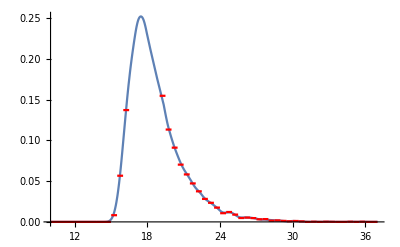

```mathematica
Show[Plot2,Plot1] (*SmoothKernelDistribution is good enough. We do not need to interpolate the acutual histogram*)
```

```mathematica
fun1αphase[x_,y_]=1/(√(2*π)*Exp[y])*Exp[-x^2/(2Exp[2*y])]
```

(ⅇ^(-1/2 ⅇ^(-2 y) x^2-y))/(√(2 π))

```mathematica
ϕdotSqLogSample=Prepend[10^Range[-1,11,0.1],0]
```

{0,0.1,0.125893,0.158489,0.199526,0.251189,0.316228,0.398107,0.501187,0.630957,0.794328,1.,1.25893,1.58489,1.99526,2.51189,3.16228,3.98107,5.01187,6.30957,7.94328,10.,12.5893,15.8489,19.9526,25.1189,31.6228,39.8107,50.1187,63.0957,79.4328,100.,125.893,158.489,199.526,251.189,316.228,398.107,501.187,630.957,794.328,1000.,1258.93,1584.89,1995.26,2511.89,3162.28,3981.07,5011.87,6309.57,7943.28,10000.,12589.3,15848.9,19952.6,25118.9,31622.8,39810.7,50118.7,63095.7,79432.8,100000.,125893.,158489.,199526.,251189.,316228.,398107.,501187.,630957.,794328.,1.×10^6,1.25893×10^6,1.58489×10^6,1.99526×10^6,2.51189×10^6,3.16228×10^6,3.98107×10^6,5.01187×10^6,6.30957×10^6,7.94328×10^6,1.×10^7,1.25893×10^7,1.58489×10^7,1.99526×10^7,2.51189×10^7,3.16228×10^7,3.98107×10^7,5.01187×10^7,6.30957×10^7,7.94328×10^7,1.×10^8,1.25893×10^8,1.58489×10^8,1.99526×10^8,2.51189×10^8,3.16228×10^8,3.98107×10^8,5.01187×10^8,6.30957×10^8,7.94328×10^8,1.×10^9,1.25893×10^9,1.58489×10^9,1.99526×10^9,2.51189×10^9,3.16228×10^9,3.98107×10^9,5.01187×10^9,6.30957×10^9,7.94328×10^9,1.×10^10,1.25893×10^10,1.58489×10^10,1.99526×10^10,2.51189×10^10,3.16228×10^10,3.98107×10^10,5.01187×10^10,6.30957×10^10,7.94328×10^10,1.×10^11}

```mathematica
fun1ϕdotphaseTable[y_]=Table[{ϕdotSqLogSample[[i]],fun1αphase[ϕdotSqLogSample[[i]],y]},{i,1,Length[ϕdotSqLogSample]}];
```

```mathematica
ϕdotSqLogFinalPDFPhase=Table[{fun1ϕdotphaseTable[y][[i,1]],NIntegrate[fun1ϕdotphaseTable[y][[i,2]]*𝒟logϕdotSq3[y],{y,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]},{i,1,Length[fun1ϕdotphaseTable[y]]}]
```

{{0,1.04564×10^-8},{0.1,1.04564×10^-8},{0.125893,1.04564×10^-8},{0.158489,1.04564×10^-8},{0.199526,1.04564×10^-8},{0.251189,1.04564×10^-8},{0.316228,1.04564×10^-8},{0.398107,1.04564×10^-8},{0.501187,1.04564×10^-8},{0.630957,1.04564×10^-8},{0.794328,1.04564×10^-8},{1.,1.04564×10^-8},{1.25893,1.04564×10^-8},{1.58489,1.04564×10^-8},{1.99526,1.04564×10^-8},{2.51189,1.04564×10^-8},{3.16228,1.04564×10^-8},{3.98107,1.04564×10^-8},{5.01187,1.04564×10^-8},{6.30957,1.04564×10^-8},{7.94328,1.04564×10^-8},{10.,1.04564×10^-8},{12.5893,1.04564×10^-8},{15.8489,1.04564×10^-8},{19.9526,1.04564×10^-8},{25.1189,1.04564×10^-8},{31.6228,1.04564×10^-8},{39.8107,1.04564×10^-8},{50.1187,1.04564×10^-8},{63.0957,1.04564×10^-8},{79.4328,1.04564×10^-8},{100.,1.04564×10^-8},{125.893,1.04564×10^-8},{158.489,1.04564×10^-8},{199.526,1.04564×10^-8},{251.189,1.04564×10^-8},{316.228,1.04564×10^-8},{398.107,1.04564×10^-8},{501.187,1.04564×10^-8},{630.957,1.04564×10^-8},{794.328,1.04564×10^-8},{1000.,1.04564×10^-8},{1258.93,1.04564×10^-8},{1584.89,1.04564×10^-8},{1995.26,1.04564×10^-8},{2511.89,1.04564×10^-8},{3162.28,1.04564×10^-8},{3981.07,1.04564×10^-8},{5011.87,1.04564×10^-8},{6309.57,1.04564×10^-8},{7943.28,1.04564×10^-8},{10000.,1.04564×10^-8},{12589.3,1.04564×10^-8},{15848.9,1.04564×10^-8},{19952.6,1.04564×10^-8},{25118.9,1.04564×10^-8},{31622.8,1.04564×10^-8},{39810.7,1.04564×10^-8},{50118.7,1.04563×10^-8},{63095.7,1.04562×10^-8},{79432.8,1.04561×10^-8},{100000.,1.04559×10^-8},{125893.,1.04557×10^-8},{158489.,1.04552×10^-8},{199526.,1.04545×10^-8},{251189.,1.04533×10^-8},{316228.,1.04514×10^-8},{398107.,1.04485×10^-8},{501187.,1.04439×10^-8},{630957.,1.04366×10^-8},{794328.,1.0425×10^-8},{1.×10^6,1.04068×10^-8},{1.25893×10^6,1.03781×10^-8},{1.58489×10^6,1.03334×10^-8},{1.99526×10^6,1.02639×10^-8},{2.51189×10^6,1.01573×10^-8},{3.16228×10^6,9.99649×10^-9},{3.98107×10^6,9.75957×10^-9},{5.01187×10^6,9.42175×10^-9},{6.30957×10^6,8.95999×10^-9},{7.94328×10^6,8.36057×10^-9},{1.×10^7,7.62708×10^-9},{1.25893×10^7,6.78473×10^-9},{1.58489×10^7,5.87758×10^-9},{1.99526×10^7,4.95904×10^-9},{2.51189×10^7,4.07979×10^-9},{3.16228×10^7,3.27841×10^-9},{3.98107×10^7,2.57783×10^-9},{5.01187×10^7,1.98704×10^-9},{6.30957×10^7,1.50484×10^-9},{7.94328×10^7,1.12303×10^-9},{1.×10^8,8.28749×10^-10},{1.25893×10^8,6.06677×10^-10},{1.58489×10^8,4.41477×10^-10},{1.99526×10^8,3.19621×10^-10},{2.51189×10^8,2.30241×10^-10},{3.16228×10^8,1.65053×10^-10},{3.98107×10^8,1.17847×10^-10},{5.01187×10^8,8.39559×10^-11},{6.30957×10^8,5.982×10^-11},{7.94328×10^8,4.26966×10^-11},{1.×10^9,3.05307×10^-11},{1.25893×10^9,2.18569×10^-11},{1.58489×10^9,1.56553×10^-11},{1.99526×10^9,1.12116×10^-11},{2.51189×10^9,8.02109×10^-12},{3.16228×10^9,5.7273×10^-12},{3.98107×10^9,4.07948×10^-12},{5.01187×10^9,2.89946×10^-12},{6.30957×10^9,2.05749×10^-12},{7.94328×10^9,1.45793×10^-12},{1.×10^10,1.0314×10^-12},{1.25893×10^10,7.28531×10^-13},{1.58489×10^10,5.13941×10^-13},{1.99526×10^10,3.62024×10^-13},{2.51189×10^10,2.54691×10^-13},{3.16228×10^10,1.7939×10^-13},{3.98107×10^10,1.27063×10^-13},{5.01187×10^10,9.07864×10^-14},{6.30957×10^10,6.52926×10^-14},{7.94328×10^10,4.69012×10^-14},{1.×10^11,3.33839×10^-14}}

```mathematica
ϕdotSqLogFinalPDFPhaseInterp=Interpolation[ϕdotSqLogFinalPDFPhase]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalization=NIntegrate[ϕdotSqLogFinalPDFPhaseInterp[x],{x,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]
```

0.492643

```mathematica
ϕdotSqLogFinalPDFPhaseNorm=Table[{ϕdotSqLogFinalPDFPhase[[i,1]],ϕdotSqLogFinalPDFPhase[[i,2]]/ϕdotSqNormalization},{i,1,Length[ϕdotSqLogFinalPDFPhase]}];
```

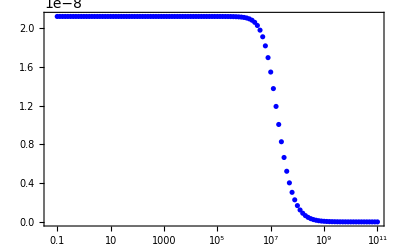

```mathematica
plotϕdotSqFinalPDFPhaseLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFPhaseNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFPhaseInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFPhaseNorm=Table[{ϕdotSqLogSample[[i]],NIntegrate[ϕdotSqFinalPDFPhaseInterpLogNorm[x],{x,Min[ϕdotSqLogSample],ϕdotSqLogSample[[i]]}]},{i,1,Length[ϕdotSqLogSample]}];
```

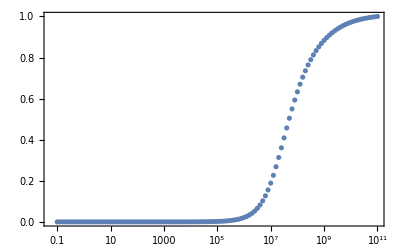

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFPhaseNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFPhaseNormInterp=Interpolation[ϕdotSqFinalCDFPhaseNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLphase=x/.FindRoot[ϕdotSqFinalCDFPhaseNormInterp[x]==0.9,{x,10^8}]
```

1.32303×10^9

```mathematica
√ϕdotSq90CLphase//ScientificForm (*90% CL upper bound on scalar-tensor from phase*)
```

3.63735×10^4

```mathematica
ϕ̇ from amplitude correction:
```

```mathematica
LogSquaredϕdotamp=Log[ϕdotSquaredamp]
```

{23.6999,23.3921,18.2859,26.7399,23.291,17.4375,20.5093,18.8404,22.1408,16314,18.4531,16.8583,19.4129,18.9372,19.0948,19.2914,20.0373,17.7558,18.8571}
 |  |  |  |

```mathematica
Min[LogSquaredϕdotamp]
```

16.3929

```mathematica
Max[LogSquaredϕdotamp]
```

37.5293

```mathematica
Histogram[LogSquaredϕdotamp];
```

```mathematica
𝒟logϕdotSqamp=SmoothKernelDistribution[LogSquaredϕdotamp]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSqamp2=PDF[𝒟logϕdotSqamp,x]
```

Piecewise[{{InterpolatingFunction[…][x], 15.1508≤x≤38.7714}, {0, True}}]

```mathematica
𝒟logϕdotSqamp3[x_]=𝒟logϕdotSqamp2
```

Piecewise[{{InterpolatingFunction[…][x], 15.1508≤x≤38.7714}, {0, True}}]

```mathematica
Plot2=Plot[𝒟logϕdotSqamp3[x],{x,7,40},PlotRange->All];
```

```mathematica
ϕdotSqLogSampleamp=Prepend[10^Range[-1,11,0.1],0];
```

```mathematica
fun1ϕdotampTable[y_]=Table[{ϕdotSqLogSampleamp[[i]],fun1αphase[ϕdotSqLogSampleamp[[i]],y]},{i,1,Length[ϕdotSqLogSampleamp]}];
```

```mathematica
ϕdotSqLogFinalPDFamp=Table[{fun1ϕdotampTable[y][[i,1]],NIntegrate[fun1ϕdotampTable[y][[i,2]]*𝒟logϕdotSqamp3[y],{y,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]},{i,1,Length[fun1ϕdotampTable[y]]}]
```

{{0,2.18×10^-9},{0.1,2.18×10^-9},{0.125893,2.18×10^-9},{0.158489,2.18×10^-9},{0.199526,2.18×10^-9},{0.251189,2.18×10^-9},{0.316228,2.18×10^-9},{0.398107,2.18×10^-9},{0.501187,2.18×10^-9},{0.630957,2.18×10^-9},{0.794328,2.18×10^-9},{1.,2.18×10^-9},{1.25893,2.18×10^-9},{1.58489,2.18×10^-9},{1.99526,2.18×10^-9},{2.51189,2.18×10^-9},{3.16228,2.18×10^-9},{3.98107,2.18×10^-9},{5.01187,2.18×10^-9},{6.30957,2.18×10^-9},{7.94328,2.18×10^-9},{10.,2.18×10^-9},{12.5893,2.18×10^-9},{15.8489,2.18×10^-9},{19.9526,2.18×10^-9},{25.1189,2.18×10^-9},{31.6228,2.18×10^-9},{39.8107,2.18×10^-9},{50.1187,2.18×10^-9},{63.0957,2.18×10^-9},{79.4328,2.18×10^-9},{100.,2.18×10^-9},{125.893,2.18×10^-9},{158.489,2.18×10^-9},{199.526,2.18×10^-9},{251.189,2.18×10^-9},{316.228,2.18×10^-9},{398.107,2.18×10^-9},{501.187,2.18×10^-9},{630.957,2.18×10^-9},{794.328,2.18×10^-9},{1000.,2.18×10^-9},{1258.93,2.18×10^-9},{1584.89,2.18×10^-9},{1995.26,2.18×10^-9},{2511.89,2.18×10^-9},{3162.28,2.18×10^-9},{3981.07,2.18×10^-9},{5011.87,2.18×10^-9},{6309.57,2.18×10^-9},{7943.28,2.18×10^-9},{10000.,2.18×10^-9},{12589.3,2.18×10^-9},{15848.9,2.18×10^-9},{19952.6,2.18×10^-9},{25118.9,2.18×10^-9},{31622.8,2.18×10^-9},{39810.7,2.18×10^-9},{50118.7,2.18×10^-9},{63095.7,2.18×10^-9},{79432.8,2.18×10^-9},{100000.,2.17999×10^-9},{125893.,2.17999×10^-9},{158489.,2.17999×10^-9},{199526.,2.17998×10^-9},{251189.,2.17997×10^-9},{316228.,2.17995×10^-9},{398107.,2.17991×10^-9},{501187.,2.17986×10^-9},{630957.,2.17978×10^-9},{794328.,2.17966×10^-9},{1.×10^6,2.17946×10^-9},{1.25893×10^6,2.17914×10^-9},{1.58489×10^6,2.17864×10^-9},{1.99526×10^6,2.17784×10^-9},{2.51189×10^6,2.17659×10^-9},{3.16228×10^6,2.1746×10^-9},{3.98107×10^6,2.17147×10^-9},{5.01187×10^6,2.16655×10^-9},{6.30957×10^6,2.15884×10^-9},{7.94328×10^6,2.14685×10^-9},{1.×10^7,2.12841×10^-9},{1.25893×10^7,2.10046×10^-9},{1.58489×10^7,2.059×10^-9},{1.99526×10^7,1.99929×10^-9},{2.51189×10^7,1.91655×10^-9},{3.16228×10^7,1.8072×10^-9},{3.98107×10^7,1.67042×10^-9},{5.01187×10^7,1.50934×10^-9},{6.30957×10^7,1.33112×10^-9},{7.94328×10^7,1.14553×10^-9},{1.×10^8,9.62687×10^-10},{1.25893×10^8,7.91022×10^-10},{1.58489×10^8,6.36281×10^-10},{1.99526×10^8,5.01603×10^-10},{2.51189×10^8,3.88069×10^-10},{3.16228×10^8,2.95235×10^-10},{3.98107×10^8,2.21495×10^-10},{5.01187×10^8,1.64393×10^-10},{6.30957×10^8,1.21035×10^-10},{7.94328×10^8,8.85372×10^-11},{1.×10^9,6.43771×10^-11},{1.25893×10^9,4.65296×10^-11},{1.58489×10^9,3.3438×10^-11},{1.99526×10^9,2.39152×10^-11},{2.51189×10^9,1.70541×10^-11},{3.16228×10^9,1.21558×10^-11},{3.98107×10^9,8.67717×10^-12},{5.01187×10^9,6.20583×10^-12},{6.30957×10^9,4.4441×10^-12},{7.94328×10^9,3.18417×10^-12},{1.×10^10,2.28104×10^-12},{1.25893×10^10,1.63242×10^-12},{1.58489×10^10,1.16596×10^-12},{1.99526×10^10,8.30679×10^-13},{2.51189×10^10,5.90428×10^-13},{3.16228×10^10,4.18979×10^-13},{3.98107×10^10,2.96943×10^-13},{5.01187×10^10,2.10155×10^-13},{6.30957×10^10,1.48511×10^-13},{7.94328×10^10,1.04814×10^-13},{1.×10^11,7.38741×10^-14}}

```mathematica
ϕdotSqLogFinalPDFampInterp=Interpolation[ϕdotSqLogFinalPDFamp]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalizationamp=NIntegrate[ϕdotSqLogFinalPDFampInterp[x],{x,Min[ϕdotSqLogSampleamp],Max[ϕdotSqLogSampleamp]}]
```

0.484333

```mathematica
ϕdotSqLogFinalPDFampNorm=Table[{ϕdotSqLogFinalPDFamp[[i,1]],ϕdotSqLogFinalPDFamp[[i,2]]/ϕdotSqNormalizationamp},{i,1,Length[ϕdotSqLogFinalPDFamp]}]
```

{{0,4.50103×10^-9},{0.1,4.50103×10^-9},{0.125893,4.50103×10^-9},{0.158489,4.50103×10^-9},{0.199526,4.50103×10^-9},{0.251189,4.50103×10^-9},{0.316228,4.50103×10^-9},{0.398107,4.50103×10^-9},{0.501187,4.50103×10^-9},{0.630957,4.50103×10^-9},{0.794328,4.50103×10^-9},{1.,4.50103×10^-9},{1.25893,4.50103×10^-9},{1.58489,4.50103×10^-9},{1.99526,4.50103×10^-9},{2.51189,4.50103×10^-9},{3.16228,4.50103×10^-9},{3.98107,4.50103×10^-9},{5.01187,4.50103×10^-9},{6.30957,4.50103×10^-9},{7.94328,4.50103×10^-9},{10.,4.50103×10^-9},{12.5893,4.50103×10^-9},{15.8489,4.50103×10^-9},{19.9526,4.50103×10^-9},{25.1189,4.50103×10^-9},{31.6228,4.50103×10^-9},{39.8107,4.50103×10^-9},{50.1187,4.50103×10^-9},{63.0957,4.50103×10^-9},{79.4328,4.50103×10^-9},{100.,4.50103×10^-9},{125.893,4.50103×10^-9},{158.489,4.50103×10^-9},{199.526,4.50103×10^-9},{251.189,4.50103×10^-9},{316.228,4.50103×10^-9},{398.107,4.50103×10^-9},{501.187,4.50103×10^-9},{630.957,4.50103×10^-9},{794.328,4.50103×10^-9},{1000.,4.50103×10^-9},{1258.93,4.50103×10^-9},{1584.89,4.50103×10^-9},{1995.26,4.50103×10^-9},{2511.89,4.50103×10^-9},{3162.28,4.50103×10^-9},{3981.07,4.50103×10^-9},{5011.87,4.50103×10^-9},{6309.57,4.50103×10^-9},{7943.28,4.50103×10^-9},{10000.,4.50103×10^-9},{12589.3,4.50103×10^-9},{15848.9,4.50103×10^-9},{19952.6,4.50103×10^-9},{25118.9,4.50103×10^-9},{31622.8,4.50103×10^-9},{39810.7,4.50103×10^-9},{50118.7,4.50103×10^-9},{63095.7,4.50103×10^-9},{79432.8,4.50102×10^-9},{100000.,4.50102×10^-9},{125893.,4.50101×10^-9},{158489.,4.501×10^-9},{199526.,4.50099×10^-9},{251189.,4.50096×10^-9},{316228.,4.50092×10^-9},{398107.,4.50085×10^-9},{501187.,4.50075×10^-9},{630957.,4.50058×10^-9},{794328.,4.50032×10^-9},{1.×10^6,4.49991×10^-9},{1.25893×10^6,4.49926×10^-9},{1.58489×10^6,4.49822×10^-9},{1.99526×10^6,4.49658×10^-9},{2.51189×10^6,4.49398×10^-9},{3.16228×10^6,4.48988×10^-9},{3.98107×10^6,4.48342×10^-9},{5.01187×10^6,4.47325×10^-9},{6.30957×10^6,4.45734×10^-9},{7.94328×10^6,4.43259×10^-9},{1.×10^7,4.39451×10^-9},{1.25893×10^7,4.3368×10^-9},{1.58489×10^7,4.2512×10^-9},{1.99526×10^7,4.12792×10^-9},{2.51189×10^7,3.95709×10^-9},{3.16228×10^7,3.73132×10^-9},{3.98107×10^7,3.4489×10^-9},{5.01187×10^7,3.11632×10^-9},{6.30957×10^7,2.74836×10^-9},{7.94328×10^7,2.36517×10^-9},{1.×10^8,1.98765×10^-9},{1.25893×10^8,1.63322×10^-9},{1.58489×10^8,1.31373×10^-9},{1.99526×10^8,1.03566×10^-9},{2.51189×10^8,8.01244×10^-10},{3.16228×10^8,6.09569×10^-10},{3.98107×10^8,4.57318×10^-10},{5.01187×10^8,3.39422×10^-10},{6.30957×10^8,2.49899×10^-10},{7.94328×10^8,1.82802×10^-10},{1.×10^9,1.32919×10^-10},{1.25893×10^9,9.60692×10^-11},{1.58489×10^9,6.90393×10^-11},{1.99526×10^9,4.93776×10^-11},{2.51189×10^9,3.52115×10^-11},{3.16228×10^9,2.5098×10^-11},{3.98107×10^9,1.79157×10^-11},{5.01187×10^9,1.28131×10^-11},{6.30957×10^9,9.1757×10^-12},{7.94328×10^9,6.57434×10^-12},{1.×10^10,4.70965×10^-12},{1.25893×10^10,3.37044×10^-12},{1.58489×10^10,2.40735×10^-12},{1.99526×10^10,1.7151×10^-12},{2.51189×10^10,1.21905×10^-12},{3.16228×10^10,8.65062×10^-13},{3.98107×10^10,6.13097×10^-13},{5.01187×10^10,4.33905×10^-13},{6.30957×10^10,3.06629×10^-13},{7.94328×10^10,2.1641×10^-13},{1.×10^11,1.52527×10^-13}}

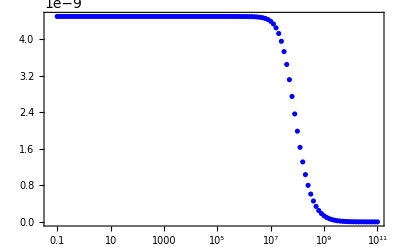

```mathematica
plotϕdotSqFinalPDFampLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFampNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFampInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFampNorm=Table[{ϕdotSqLogSampleamp[[i]],NIntegrate[ϕdotSqFinalPDFampInterpLogNorm[x],{x,Min[ϕdotSqLogSampleamp],ϕdotSqLogSampleamp[[i]]}]},{i,1,Length[ϕdotSqLogSampleamp]}];
```

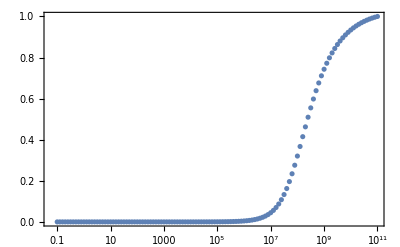

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFampNorm,PlotRange->All,PlotRange->All,Frame->True]
```

```mathematica
ϕdotSqFinalCDFampNormInterp=Interpolation[ϕdotSqFinalCDFampNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLamp=x/.FindRoot[ϕdotSqFinalCDFampNormInterp[x]==0.9,{x,10^9}]
```

5.32501×10^9

```mathematica
√ϕdotSq90CLamp//ScientificForm (*90% CL upper boun on \[Phi dot from amp*)
```

7.29727×10^4

```mathematica
Combinined upper bound:
```

```mathematica
ϕdotSquaredcomb
```

{4.09108×10^9,2.98605×10^9,1.97183×10^7,8.43546×10^10,2.73249×10^9,9.58174×10^6,1.6442×10^8,3.39587×10^7,16316,4.71798×10^6,6.04166×10^7,3.7062×10^7,4.3369×10^7,5.23318×10^7,1.2044×10^8,1.24339×10^7,3.34897×10^7}
 |  |  |  |

```mathematica
LogϕdotSquaredcomb=Log[ϕdotSquaredcomb] (*This is Log of sigma_(alpha^2)*)
```

{22.1321,21.8172,16.7971,25.1583,21.7285,16.0754,18.9179,17.3407,20.5729,16314,16.9393,15.3669,17.9168,17.4281,17.5853,17.7731,18.6067,16.3359,17.3267}
 |  |  |  |

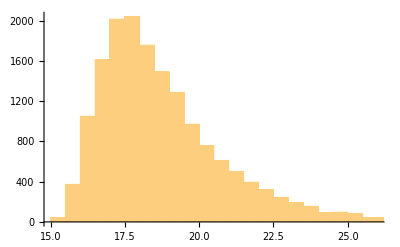

```mathematica
Histogram[LogϕdotSquaredcomb]
```

```mathematica
Min[LogϕdotSquaredcomb]
```

15.0519

```mathematica
Max[LogϕdotSquaredcomb]
```

35.9618

```mathematica
𝒟logϕdotSqcomb=SmoothKernelDistribution[LogϕdotSquaredcomb]
```

DataDistribution[…]

```mathematica
𝒟logϕdotSq2comb=PDF[𝒟logϕdotSqcomb,x]
```

Piecewise[{{InterpolatingFunction[…][x], 13.8342≤x≤37.1795}, {0, True}}]

```mathematica
𝒟logϕdotSq3comb[x_]=𝒟logϕdotSq2comb
```

Piecewise[{{InterpolatingFunction[…][x], 13.8342≤x≤37.1795}, {0, True}}]

```mathematica
fun1ϕdotcombTable[y_]=Table[{ϕdotSqLogSample[[i]],fun1αphase[ϕdotSqLogSample[[i]],y]},{i,1,Length[ϕdotSqLogSample]}];(*I am using the same sample as the phase*)
```

```mathematica
ϕdotSqLogFinalPDFcomb=Table[{fun1ϕdotcombTable[y][[i,1]],NIntegrate[fun1ϕdotcombTable[y][[i,2]]*𝒟logϕdotSq3comb[y],{y,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]},{i,1,Length[fun1ϕdotcombTable[y]]}]
```

{{0,9.67779×10^-9},{0.1,9.67779×10^-9},{0.125893,9.67779×10^-9},{0.158489,9.67779×10^-9},{0.199526,9.67779×10^-9},{0.251189,9.67779×10^-9},{0.316228,9.67779×10^-9},{0.398107,9.67779×10^-9},{0.501187,9.67779×10^-9},{0.630957,9.67779×10^-9},{0.794328,9.67779×10^-9},{1.,9.67779×10^-9},{1.25893,9.67779×10^-9},{1.58489,9.67779×10^-9},{1.99526,9.67779×10^-9},{2.51189,9.67779×10^-9},{3.16228,9.67779×10^-9},{3.98107,9.67779×10^-9},{5.01187,9.67779×10^-9},{6.30957,9.67779×10^-9},{7.94328,9.67779×10^-9},{10.,9.67779×10^-9},{12.5893,9.67779×10^-9},{15.8489,9.67779×10^-9},{19.9526,9.67779×10^-9},{25.1189,9.67779×10^-9},{31.6228,9.67779×10^-9},{39.8107,9.67779×10^-9},{50.1187,9.67779×10^-9},{63.0957,9.67779×10^-9},{79.4328,9.67779×10^-9},{100.,9.67779×10^-9},{125.893,9.67779×10^-9},{158.489,9.67779×10^-9},{199.526,9.67779×10^-9},{251.189,9.67779×10^-9},{316.228,9.67779×10^-9},{398.107,9.67779×10^-9},{501.187,9.67779×10^-9},{630.957,9.67779×10^-9},{794.328,9.67779×10^-9},{1000.,9.67779×10^-9},{1258.93,9.67779×10^-9},{1584.89,9.67779×10^-9},{1995.26,9.67779×10^-9},{2511.89,9.67779×10^-9},{3162.28,9.67779×10^-9},{3981.07,9.67779×10^-9},{5011.87,9.67779×10^-9},{6309.57,9.67779×10^-9},{7943.28,9.67778×10^-9},{10000.,9.67778×10^-9},{12589.3,9.67778×10^-9},{15848.9,9.67778×10^-9},{19952.6,9.67777×10^-9},{25118.9,9.67776×10^-9},{31622.8,9.67775×10^-9},{39810.7,9.67772×10^-9},{50118.7,9.67769×10^-9},{63095.7,9.67763×10^-9},{79432.8,9.67753×10^-9},{100000.,9.67738×10^-9},{125893.,9.67715×10^-9},{158489.,9.67678×10^-9},{199526.,9.67619×10^-9},{251189.,9.67525×10^-9},{316228.,9.67377×10^-9},{398107.,9.67142×10^-9},{501187.,9.66771×10^-9},{630957.,9.66183×10^-9},{794328.,9.65255×10^-9},{1.×10^6,9.6379×10^-9},{1.25893×10^6,9.61487×10^-9},{1.58489×10^6,9.5788×10^-9},{1.99526×10^6,9.52269×10^-9},{2.51189×10^6,9.43628×10^-9},{3.16228×10^6,9.30518×10^-9},{3.98107×10^6,9.11054×10^-9},{5.01187×10^6,8.83004×10^-9},{6.30957×10^6,8.44138×10^-9},{7.94328×10^6,7.92845×10^-9},{1.×10^7,7.28894×10^-9},{1.25893×10^7,6.53966×10^-9},{1.58489×10^7,5.71623×10^-9},{1.99526×10^7,4.86607×10^-9},{2.51189×10^7,4.03763×10^-9},{3.16228×10^7,3.27062×10^-9},{3.98107×10^7,2.59091×10^-9},{5.01187×10^7,2.01077×10^-9},{6.30957×10^7,1.53193×10^-9},{7.94328×10^7,1.14883×10^-9},{1.×10^8,8.509×10^-10},{1.25893×10^8,6.24557×10^-10},{1.58489×10^8,4.55432×10^-10},{1.99526×10^8,3.30339×10^-10},{2.51189×10^8,2.3839×10^-10},{3.16228×10^8,1.71176×10^-10},{3.98107×10^8,1.22368×10^-10},{5.01187×10^8,8.72171×10^-11},{6.30957×10^8,6.21218×10^-11},{7.94328×10^8,4.4307×10^-11},{1.×10^9,3.16628×10^-11},{1.25893×10^9,2.26597×10^-11},{1.58489×10^9,1.62287×10^-11},{1.99526×10^9,1.16242×10^-11},{2.51189×10^9,8.32049×10^-12},{3.16228×10^9,5.94585×10^-12},{3.98107×10^9,4.23881×10^-12},{5.01187×10^9,3.0147×10^-12},{6.30957×10^9,2.14023×10^-12},{7.94328×10^9,1.51723×10^-12},{1.×10^10,1.07391×10^-12},{1.25893×10^10,7.58906×10^-13},{1.58489×10^10,5.35603×10^-13},{1.99526×10^10,3.77499×10^-13},{2.51189×10^10,2.65671×10^-13},{3.16228×10^10,1.86978×10^-13},{3.98107×10^10,1.32121×10^-13},{5.01187×10^10,9.41112×10^-14},{6.30957×10^10,6.75745×10^-14},{7.94328×10^10,4.86113×10^-14},{1.×10^11,3.47308×10^-14}}

```mathematica
ϕdotSqLogFinalPDFcombInterp=Interpolation[ϕdotSqLogFinalPDFcomb]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqNormalizationcomb=NIntegrate[ϕdotSqLogFinalPDFcombInterp[x],{x,Min[ϕdotSqLogSample],Max[ϕdotSqLogSample]}]
```

0.49237

```mathematica
ϕdotSqLogFinalPDFcombNorm=Table[{ϕdotSqLogFinalPDFcomb[[i,1]],ϕdotSqLogFinalPDFcomb[[i,2]]/ϕdotSqNormalizationcomb},{i,1,Length[ϕdotSqLogFinalPDFcomb]}];
```

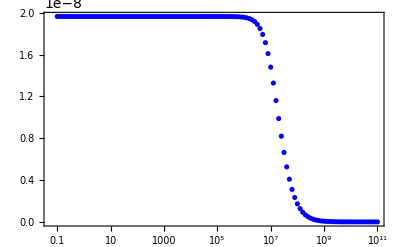

```mathematica
plotϕdotSqFinalPDFcombLogNorm=ListLogLinearPlot[{ϕdotSqLogFinalPDFcombNorm},PlotRange->All,PlotRange->All,Frame->True,PlotStyle->{Blue,Red}]
```

```mathematica
ϕdotSqFinalPDFcombInterpLogNorm=Interpolation[ϕdotSqLogFinalPDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSqFinalCDFcombNorm=Table[{ϕdotSqLogSample[[i]],NIntegrate[ϕdotSqFinalPDFcombInterpLogNorm[x],{x,Min[ϕdotSqLogSample],ϕdotSqLogSample[[i]]}]},{i,1,Length[ϕdotSqLogSample]}];
```

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True];
```

```mathematica
ϕdotSqFinalCDFcombNormInterp=Interpolation[ϕdotSqFinalCDFcombNorm]
```

InterpolatingFunction[…]

```mathematica
ϕdotSq90CLcomb=x/.FindRoot[ϕdotSqFinalCDFcombNormInterp[x]==0.9,{x,10^8}]
```

1.41998×10^9

```mathematica
√ϕdotSq90CLcomb//ScientificForm (*90% CL upper bound on scalar-tensor from combined pdf*)
```

3.76827×10^4

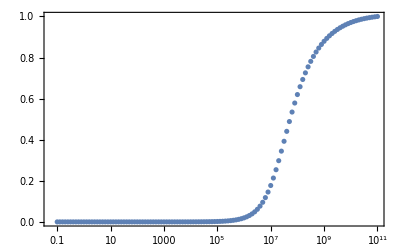

```mathematica
ListLogLinearPlot[ϕdotSqFinalCDFcombNorm,PlotRange->All,PlotRange->All,Frame->True]
```

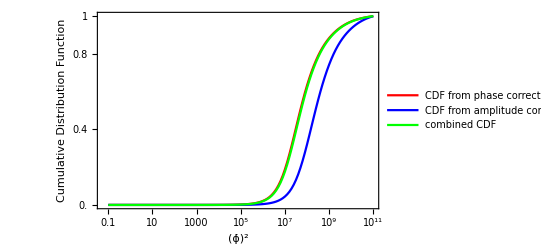

```mathematica
PlotCDFComparisonAll=ListLogLinearPlot[{ϕdotSqFinalCDFPhaseNorm,ϕdotSqFinalCDFampNorm,ϕdotSqFinalCDFcombNorm},Joined->True,PlotRange->All,PlotStyle->{Red,Blue,Green},PlotLegends->{Placed[LineLegend[{"CDF from phase correction  ","CDF from amplitude correction","combined CDF"},LabelStyle->{Orange,FontSize->5},LegendMarkerSize->8,LegendMargins->0,LegendFunction->"Frame"],{Right,Bottom}]},FrameLabel->{"(ϕ̇)^2","Cumulative Distribution Function"},FrameStyle->Directive[Gray,Dashed],Frame->True,FrameTicks->{Automatic,{0.0,0.2,0.4,0.6,0.8,0.9,1}},FrameTicksStyle->Directive[Black,9]]
```

## Small Coupling Approximation:

```mathematica
𝒟logphase=HistogramDistribution[Log[m1*√(1.64485*ϕdotSquared)]]
```

DataDistribution[…]

```mathematica
Max[Log[m1*√(1.64485*ϕdotSquared)]]
```

9.49346

```mathematica
ps1=PDF[𝒟logphase,x];
ps2[x]=ps1;
```

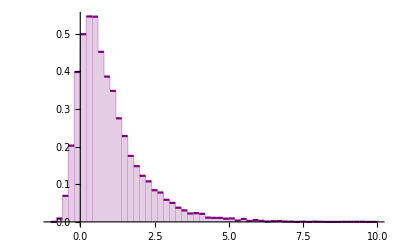

```mathematica
Plot[ps2[x],{x,-1,10},Filling->Axis,PlotStyle->Purple,PlotRange->All]
```

```mathematica
Integrate[ps2[x],{x,Log[Min[m1*√(1.64485*ϕdotSquared)]],Log[Max[m1*√(1.64485*ϕdotSquared)]]}]
```

0.999422

```mathematica
Integrate[ps2[x],{x,Log[Min[m1*√1.64485*√ϕdotSquared]],0}]*100 (*11% satisfies small coupling approximation*)
```

13.5261

```mathematica
𝒟logamp=HistogramDistribution[Log[m1*√1.64485*√ϕdotSquaredamp]]
```

DataDistribution[…]

```mathematica
ps1amp=PDF[𝒟logamp,x];
ps2amp[x]=ps1amp;
```

```mathematica
Min[Log[m1*√1.64485*√ϕdotSquaredamp]]
```

0.00158844

```mathematica
Max[Log[m1*√ϕdotSquaredamp*√1.64485]]
```

10.3177

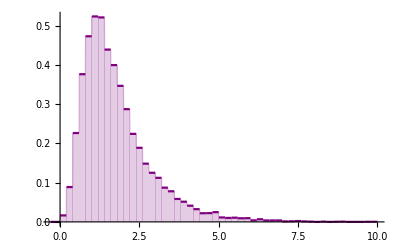

```mathematica
Plot[ps2amp[x],{x,-0.3,10},Filling->Axis,PlotStyle->Purple,PlotRange->All]
```

```mathematica
Integrate[ps2amp[x],{x,Log[Min[m1*√1.64485*√ϕdotSquaredamp]],Log[Max[m1*√1.64485*√ϕdotSquaredamp]]}]
```

0.999949

```mathematica
Integrate[ps2amp[x],{x,Log[Min[m1*√1.64485*√ϕdotSquaredamp]],0}]*100 (*None of the data satisfies small coupling approximation*)
```

-0.002626

Check for other events:

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->1.46,m2t->1.27,s1t->1,s2t->1,ηt->(1.46*1.27/(1.46+1.27)^2)} (*GW170608*)
```

1.9214

```mathematica
((10^-4*1792/5 ηt^(-2/5))/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->50.6,m2t->34.3,s1t->1,s2t->1,ηt->(50.6*34.3/(50.6+34.3)^2)} (*GW170729*)
```

0.781306

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->35.6,m2t->30.6,s1t->1,s2t->1,ηt->(35.6*30./(35.6+30.6)^2)}  (*GW150914*)
```

1.78769

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->13.7,m2t->7.7,s1t->1,s2t->1,ηt->(13.7*7.7/(13.7+7.7)^2)}  (*GW151226*)
```

0.579798

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->23.3,m2t->13.6,s1t->1,s2t->1,ηt->(23.3*13.6/(23.3+13.6)^2)}  (*GW151012*)
```

0.608695

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->39.6,m2t->29.4,s1t->1,s2t->1,ηt->(39.6*29.4/(39.6+29.4)^2)}  (*GW170823*)
```

0.974115

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->35.5,m2t->26.4,s1t->1,s2t->1,ηt->(35.5*26.8/(35.5+26.8)^2)}  (*GW170818*)
```

0.978348

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->30.7,m2t->25.3,s1t->1,s2t->1,ηt->(30.7*25.3/(30.7+25.3)^2)}  (*GW170814*)
```

1.42283

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->35.2,m2t->23.8,s1t->1,s2t->1,ηt->(35.2*25.8/(35.2+25.8)^2)}  (*GW170809*)
```

0.775035

```mathematica
((ηt^(-2/5)10^-4*1792/5)/((m1t*s1t)-(m2t*s2t))^2)^(1/2)*m1t/.{m1t->31.,m2t->20.1,s1t->1,s2t->1,ηt->(31*20.1/(31+20.1)^2)}  (*GW170104*)
```

0.717094